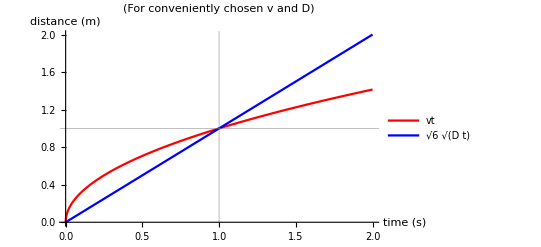

```mathematica
(*p[N_,x_] := (1/2)*(1/(N*x) + 1/(1-x))
f[N_,x_,chi_] := (1/N)*x*Log[x] + (1-x)*Log[1-x] + chi*x*(1-x)

a= Plot[p[10,x],{x,0,1},AxesLabel->{Style["ϕ",14],Style["χ(ϕ)",14]},BaseStyle->{FontFamily->"Times New Roman",FontSize->8},Axes->True,PlotStyle->{{Blue,Thickness[.002]}}];
b= Plot[p[20,x],{x,0,1},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->8},Axes->True,PlotStyle->{{Blue,Thickness[.002]}},Frame->True,FrameLabel->{Style["ϕ",10],Style["χ(ϕ)",10]},PlotLabel->"Polymer Spinodal"];
c= Plot[{f[100,x,.4],f[100,x,.5],f[100,x,.6]},{x,0,1},Axes->True,PlotStyle->{{Blue,Thickness[.002]},{Red,Thickness[.002]},{Green,Thickness[.002]}},Frame->True,FrameLabel->{Style["ϕ",10],Style["f(ϕ)",10]},FrameStyle->{FontFamily->"Latin Modern Roman",FontSize->8}, PlotLabel->"Polymer Free Energy",PlotLegends->LineLegend[{"χ = .4","χ = .5","χ = .6"}],LabelStyle->{FontSize->10}];
(*d= Plot[f[100,x,.5],{x,0,1},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->8},Axes->True,PlotStyle->{{Red,Thickness[.002]}},Frame->True,FrameLabel->{Style["ϕ",10],Style["f(ϕ)",10]},PlotLabel->"Polymer Free Energy"];
e = Plot[f[100,x,.6],{x,0,1},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->8},Axes->True,PlotStyle->{{Green,Thickness[.002]}},Frame->True,FrameLabel->{Style["ϕ",10],Style["f(ϕ)",10]},PlotLabel->"Polymer Free Energy"];*)
Export["fPlot.pdf",%]
Show[c]*)
ClearAll["Global`*"]
a = Plot[{Sqrt[t],t},{t,0,2},PlotStyle->{{Red},{Blue}},AxesLabel->{Style["time (s)",14, FontColor->Black],Style["distance (m)",14,FontColor->Black]},GridLines->{{1,1}},PlotLegends->{Style[vt, 16],Style[FullSimplify[Sqrt[(6D)t]],16]},PlotLabel->Style["
(For conveniently chosen v and D)",14]]

(*Energy[c_,a_] := a*Sqrt[1-(a^2)*c^2] +(a^2)* c^2
Solve[D[Energy[c,a],c]==0,{c}];
D[D[Energy[c,a],c],c];
Reduce[2 a^2-(a^5 c^2)/((1-a^2 c^2)^(3/2))-a^3/(√(1-a^2 c^2))<0,{c}]
 a= Plot[Energy[c,1],{c,0,1},AxesStyle->Black,GridLines->Automatic,AxesLabel->{Style["(2κ + κ_G)/λ C",14, FontColor->Red],Style["E/E_sphere",14,FontColor->Red]},BaseStyle->{FontFamily->"Times New Roman",FontSize->12},Axes->True,PlotStyle->{{Blue,Thickness[.002]}}];*)
```